# Testarea I-a la "Paradigme de Programare"

## Curmanschii Anton, MIA2201

Facultatea de Matematică și Informatică
Specialitatea Informatică Aplicată
Varianta 3

```mathematica
n=3
```

3

## 3. Calcularea limitelor

```mathematica
lim_(k->∞) (1/(k n)+1)^k
```

ⅇ^(1/3)

```mathematica
lim_(k->∞) (∑_(l=1)^n l/k^(n/7))
```

0

```mathematica
lim_(k->∞) n/ⅇ^k
```

0

## 4. Calcularea sumelor seriei

```mathematica
∑_(k=1)^∞ n/k^n
```

3 Zeta[3]

```mathematica
∑_(k=1)^∞ (sin (k n))/k^n
```

(π^2 sin)/2

```mathematica
∑_(k=2)^∞ n/Log[k]
```

Sum::div: Sum does not converge.

## 5. Calcularea produsului

```mathematica
∏_(k=1)^(3 n) k
```

362880

## 7. Calcularea derivatelor de ordinul n ale funcțiilor

```mathematica
f0[x_]:=x^(2 n);
```

```mathematica
d0=f0'''[x]
```

120 x^3

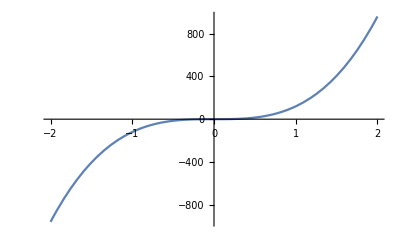

```mathematica
Plot[d0,{x,-2,2}]
```

```mathematica
f1[x_] :=Sin[n x];
```

```mathematica
d1 = f1'''[x]
```

-27 Cos[3 x]

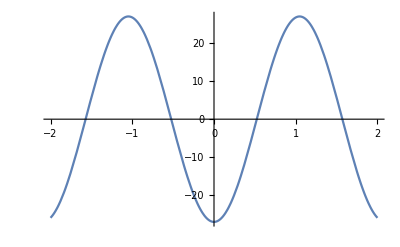

```mathematica
Plot[d1,{x, -2, 2}]
```

```mathematica
f2[x_]:=Log@Abs[x+1]
```

```mathematica
d2 = f2'''[x]
```

(2 Abs'[1+x]^3)/Abs[1+x]^3-(3 Abs'[1+x] Abs''[1+x])/Abs[1+x]^2+(Abs^(3)[1+x])/Abs[1+x]

Notez, că Wolfram nu poate deriva funcția Abs.

```mathematica
Plot[d2, {x,-10,10}]
```

-Graphics-

## 8. Calcularea derivatelor mixte ale funcțiilor de două variabilă

```mathematica
derivate[f_]:=Derivative[2,3][f][x,y]
```

```mathematica
Clear[f0,f1,f2]
```

```mathematica
f0[x_,y_]:= x^(2 n)Sin[y]
```

```mathematica
d0=derivate[f0]
```

```mathematica
-30 x^4 Cos[y]
```

```mathematica
Plot3D[d0,{x,-2,2},{y,-2,2}]
```

-Graphics3D-

```mathematica
f1[x_,y_]:=E^y Sin[n x^2]
```

```mathematica
d1=derivate[f1]
```

6 ⅇ^y Cos[3 x^2]-36 ⅇ^y x^2 Sin[3 x^2]

```mathematica
Plot3D[d1, {x,10,20},{y,10,20}]
```

-Graphics3D-

```mathematica
f2[x_,y_]:=Log[Abs[x+y]^n]
```

```mathematica
d2=derivate[f2]
```

(72 Abs'[x+y]^5)/Abs[x+y]^5-(180 Abs'[x+y]^3 Abs''[x+y])/Abs[x+y]^4+(90 Abs'[x+y] Abs''[x+y]^2)/Abs[x+y]^3+(60 Abs'[x+y]^2 Abs^(3)[x+y])/Abs[x+y]^3-(30 Abs''[x+y] Abs^(3)[x+y])/Abs[x+y]^2-(15 Abs'[x+y] Abs^(4)[x+y])/Abs[x+y]^2+(3 Abs^(5)[x+y])/Abs[x+y]

Notez, că Wolfram nu poate deriva funcția Abs.

```mathematica
Plot3D[f2,{x,-2,2},{y,-2,2}]
```

-Graphics3D-

## 9. Calcularea integralelor

```mathematica
∫x^n ⅆx
```

x^4/4

```mathematica
∫_n^(2 n) Sin[x]ⅆx
```

Cos[3]-Cos[6]

## 11. Rezolvarea sistemelor de ecuații

```mathematica
Solve[x+y==n&&x-y==-n,{x,y}]
```

```mathematica
{{x->0,y->3}}
```

```mathematica
Solve[x^n+n x == n,x]
```

{{x→Root0.818Root[-3+3 #1+#1^3&,1]0.8177316738868234},{x→Root-0.409-1.87 ⅈRoot[-3+3 #1+#1^3&,2]-0.4088658369434118},{x→Root-0.409+1.87 ⅈRoot[-3+3 #1+#1^3&,3]-0.4088658369434118}}

```mathematica
Reduce[x+2y>=n&&-x+y<=-n,{x,y}]
```

(x==3&&y==0)||(x>3&&(3-x)/2≤y≤-3+x)

## 12. Sumarea elementelor în diferite moduri

### În mod procedural

```mathematica
list=Range[n,50000 n]
```

{3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,149954,149979,149980,149981,149982,149983,149984,149985,149986,149987,149988,149989,149990,149991,149992,149993,149994,149995,149996,149997,149998,149999,150000}
 |  |  |  |

```mathematica
sum = 0;
listLength = Length[list]
{t,void}=AbsoluteTiming@For[i=1,i<=listLength,i++,sum=list[[i]]+sum];
t 
sum
```

149998

0.309265

11250074997

### În mod funcțional

```mathematica
{t,sum}=AbsoluteTiming@Fold[(#1+#2)&,list];
t
sum
```

0.0222604

11250074997

### Funcția standard

```mathematica
{t,sum}=AbsoluteTiming@Total[list];
t
sum
```

0.0003019

11250074997